```mathematica
(*початкові дані*)
f[x1_,x2_]=x1^4 +x2^4-2 x1^2-4x1 x2 -2 x2^2;
X0={1.,-1.}; 
ϵ=10^-30;
Plot3D[f[x1,x2],{x1,-10,10},{x2,-10,10},MeshFunctions->{#3&},Mesh->50]
```

-Graphics3D-

```mathematica
(*функція, яка повертатиме значення градієнта в точці*)
Gr[f_,X0_]:=Grad[f[x1,x2],{x1,x2}]/.Thread[{x1,x2}->X0]
(*функція, яка повертає гессіан функції в точці*)
H[f_,X0_]:=({{D[f[x1,x2],{x1,2}], D[f[x1,x2],x1,x2]}, {D[f[x1,x2],x2,x1], D[f[x1,x2],{x2,2}]}})/.Thread[{x1,x2}->X0];
(*метод спряжених напрямків*)
ConjugateGradientMethod[f_,x0_,ϵ_,modification_?(MemberQ[{1,2},#]&),flag_?BooleanQ]:=(
t0=Now;
k=0;
p={};
X={x0};
res1={{"k","x1^(k + 1)","x2^(k + 1)","f((x̄)^(k + 1))","α^(k)","β^(k)","p_1^(k)","p_2^(k)","‖∇f((x̄)^(k))‖"}};

While[Norm[Gr[f,X[[-1]]]]≥ϵ,{
If[k≥8,Break[]];
(* обчислення β *)
Switch[modification,
1,
If[k==0,β=0,β=(Gr[f,X[[-1]]].Gr[f,X[[-1]]])/(Gr[f,X[[-2]]].Gr[f,X[[-2]]]) Mod[k,2]],
2,
If[k==0,β=0,β=(Gr[f,X[[-1]]].(Gr[f,X[[-1]]]-Gr[f,X[[-2]]]))/(Gr[f,X[[-2]]].Gr[f,X[[-2]]]) Mod[k,2]]
];
(* обчислення p *)
If[k==0,
AppendTo[p,-Gr[f,X[[-1]]]],AppendTo[p,-Gr[f,X[[-1]]]+β p[[-1]]]
];

(* пошук α *)
ff[Α_]=f[X[[-1,1]]+Α p[[-1,1]],X[[-1,2]]+Α p[[-1,2]]];
α=NMinimize[ff[Α],Α][[2,1,2]];


(* обчислення x^(k+1) *)
AppendTo[X,X[[-1]]+α p[[-1]]];

(*додавання в масив дані про ітерацію*)
AppendTo[res1,{k,X[[-1,1]],X[[-1,2]],f[X[[1,-1]],X[[2,-1]]],α,β,p[[-1,1]],p[[-1,2]],Norm[Gr[f,X[[-1]]]]}];

k++
}];
t1=Now;
If[flag,{
Print["Таблиця результатів: \n",Grid[res1]];
Print["Час роботи методу: ",t=t1-t0, "\nНев'язка: ",Norm[min-X[[-1]] ],"\nПохибка: ",Abs[f[min[[1]],min[[2]]]-f[X[[-1,1]],X[[-1,2]]]],"\nОтримане значення: ",X[[-1]],"\nЗначення функції: ",f[X[[-1,1]],X[[-1,2]]]];
r=2;
Print[Show[ContourPlot[f[x1,x2],{x1,-2,2},{x2,-2,1},ContourShading->None,Contours->{Automatic,50}],Graphics[{Green,PointSize[0.015],Point[X],Blue,PointSize[0.025],Point[X[[1]]],Gray,PointSize[0.025],Opacity[0.5],Point[min]}],ListLinePlot[X,ColorFunction->Function[{x,y},Hue[y]]]]];
}];
Return[X[[-1]]])
```

формула Полака-Райбера

Таблиця результатів: 
k | x1^(k + 1) | x2^(k + 1) | f((x̄)^(k + 1)) | α^(k) | β^(k) | p_1^(k) | p_2^(k) | ‖∇f((x̄)^(k))‖
0 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | 0.25 | 0 | -4. | 4. | 2.56313×10^-21
1 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | 10.3916 | 2.05301×10^-43 | 1.79995×10^-21 | -1.82479×10^-21 | 2.9773×10^-21
2 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | 2.55655 | 0. | 7.41154×10^-22 | -2.88358×10^-21 | 3.26111×10^-20
3 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | 1.49947 | 119.973 | 6.77429×10^-20 | -3.70753×10^-19 | 2.60272×10^-18
4 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | -1.66798 | 0. | -1.83859×10^-18 | -1.84222×10^-18 | 3.21275×10^-17
5 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | -30.4765 | 152.369 | -2.57425×10^-16 | -2.57981×10^-16 | 8.88888×10^-14
6 | -7.70043×10^-8 | 7.69578×10^-8 | -1. | -369.743 | 0. | 6.28538×10^-14 | 6.28538×10^-14 | 2.62839×10^-10
7 | -1.41421 | -1.41421 | -1. | -2.5742×10^6 | 8.74353×10^6 | 5.49379×10^-7 | 5.49379×10^-7 | 4.00245×10^-6

Час роботи методу: 0.360899 s
Нев'язка: 5.05332×10^-6
Похибка: 2.02712×10^-10
Отримане значення: {-1.41421,-1.41421}
Значення функції: -8.

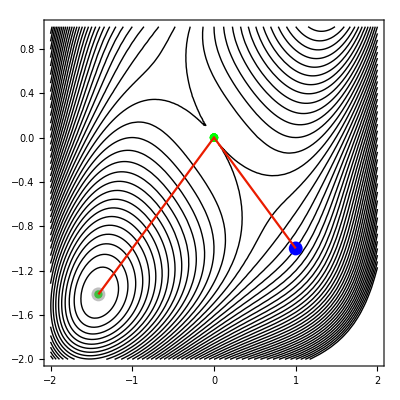

формула Флетчера-Рівса

Таблиця результатів: 
k | x1^(k + 1) | x2^(k + 1) | f((x̄)^(k + 1)) | α^(k) | β^(k) | p_1^(k) | p_2^(k) | ‖∇f((x̄)^(k))‖
0 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | 0.25 | 0 | -4. | 4. | 2.56313×10^-21
1 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | 6.00776 | 4.53091×10^-22 | -1.24202×10^-23 | -1.24202×10^-23 | 2.72183×10^-21
2 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | 6.16085 | 0. | 1.16467×10^-21 | -2.46006×10^-21 | 4.61325×10^-20
3 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | 1.61763 | 280.69 | 2.96154×10^-19 | -7.24897×10^-19 | 3.96944×10^-18
4 | -7.69811×10^-8 | 7.69811×10^-8 | -1. | -3.3964 | 0. | -2.805×10^-18 | -2.80863×10^-18 | 1.03885×10^-16
5 | -7.69804×10^-8 | 7.69817×10^-8 | -1. | -326.066 | 711.102 | -1.92118×10^-15 | -1.92377×10^-15 | 7.09215×10^-12
6 | -7.88347×10^-8 | 7.51275×10^-8 | -1. | -369.743 | 0. | 5.01491×10^-12 | 5.01491×10^-12 | 2.09711×10^-8
7 | -1.41421 | -1.41421 | -1. | -32252.6 | 8.74649×10^6 | 0.000043848 | 0.000043848 | 2.63768×10^-6

Час роботи методу: 0.366354 s
Нев'язка: 5.05157×10^-6
Похибка: 2.02902×10^-10
Отримане значення: {-1.41421,-1.41421}
Значення функції: -8.

-Graphics-

```mathematica
min={-1.41421,-1.41421};
Print["формула Полака-Райбера"];
ConjugateGradientMethod[f,X0,ϵ,1,True];
Print["формула Флетчера-Рівса"];
ConjugateGradientMethod[f,X0,ϵ,2,True];
```